## Peak finder

```mathematica
img=Import["~/Dropbox/projects/pigun/testimgs/flp/img2.png"];
tmp=ImageData[img];
Length[tmp]
Length[tmp[[1]]]
img=ImageResize[img,{Length[tmp[[1]]]/2,Length[tmp]/2}];
img=ImageData[img];
img=0.299img[[All,All,1]]+0.587img[[All,All,2]]+0.114img[[All,All,3]];
```

720

1280

```mathematica
MatrixPlot[img,ColorFunction->GrayLevel]
```

-Graphics-

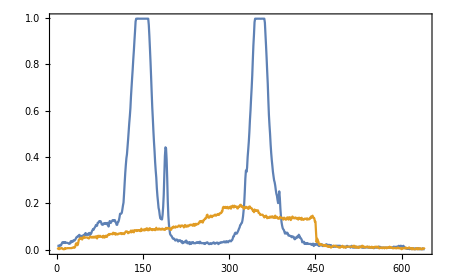

```mathematica
ListPlot[img[[{130,200}]],PlotRange->All]
```

```mathematica
ny=Length[img[[1]]];
nx=Length[img];
peaks={{-1,1,0,0,0},{-1,ny,0,0,0}};
t=0.5;

For[i=1,i≤nx,i++,(* i/x is for rows *)

status=0;
linesumx=0;
linesumy=0;

For[j=1,j≤ny,j++,(* j/y is for columns *)

If[status<0,
status++;
Continue[];
];

px=img[[i,j]];

If[px>t && status==0,(* start recording the histogram *)
status=1;
linesumy=0;linesumx=0;
];
If[px>t && status==1,(* record the histogram *)
linesumx+=px;
linesumy+=px*j;
];
If[px≤t && status==1, (* stop recording, peak ended *)
status=-5;(* enable record starting again after 5 pixels at least *)
(* store the partial result somewhere *)
total=linesumx;
(*linesumx*=i/total;
linesumy/=total;*)
thisY=linesumy/total;

(*Print[{"peak done:",i,linesumx,linesumy}];*)
(* update info in pID? *)
(* which peak is the closest in y to the *)
dists={0,0};
dists[[1]]=Abs[peaks[[1,2]]-thisY];
dists[[2]]=Abs[peaks[[2,2]]-thisY];
If[dists[[1]]<dists[[2]],pID=1;,pID=2;];(* get the closest peak *)
peaks[[pID,3]]+=total;
peaks[[pID,4]]+=linesumx*i;
peaks[[pID,5]]+=linesumy;
peaks[[pID,2]]=thisY;

];


];(* end of loop over j *)

];(* end of loop over i *)
peaks[[All,1]]=peaks[[All,4]]/peaks[[All,3]]
peaks[[All,2]]=peaks[[All,5]]/peaks[[All,3]]
peaks
```

{132.402,125.412}

{148.023,352.915}

{{132.402,148.023,1114.19,147522.,164926.},{125.412,352.915,853.761,107072.,301305.}}

```mathematica
tmp=peaks[[All,{2,1}]];
tmp={#[[1]],(360-#[[2]])}&/@tmp;
Show[{ListDensityPlot[Reverse[img]]
,ListPlot[tmp,Joined->False,PlotStyle->Red]
}]
```

-Graphics-

## Positioning

```mathematica
org={0,0,0};
h=0.1;(* distance between LED and center of bar *)
leds={org-{h,0,0},org+{h,0,0}};(* LED positions *)
p={0,-2.5,0}; (* position of the shooter *)
arm=0.6;(* length of the arm *)
armdir={0.01,1,0};armdir/=Norm[armdir];
```

```mathematica
Show[{
ListPointPlot3D[{org}, PlotStyle->Directive[{Black,PointSize[Medium]}]],
ListPointPlot3D[leds, PlotStyle->Directive[{Red,PointSize[Medium]}]],
ListPointPlot3D[{p}, PlotStyle->Directive[{Blue,PointSize[Medium]}]],
Graphics3D[{Arrow[{p,p+armdir}]}]
},PlotRange->All]
```

-Graphics3D-

## Misc Geometry

What is shown here:

1) we put the LED bar center in the origin, aligned along the x axis
2) the gun (viewpoint) sees the two LEDS at a given angle γ
3) the gun is located at some point (d,θ) in polar coordinates
4) we find the distance d that satisfies (2)

```mathematica
org={0,0,0};
h=0.1;(* distance between LED and center of bar *)
leds={org-{h,0,0},org+{h,0,0}};(* LED positions *)
```

```mathematica
p=d{Cos[θ],Sin[θ],0}; (* gun position *)
v=(#-p)&/@leds;(* vectors gun->LEDs *)
eq=v[[1]].v[[2]]/(Norm[v[[1]]]Norm[v[[2]]]);
sol=Solve[eq==Cos[γ],d];

γ0=Pi/4;

data=Table[
s=sol/.{γ->γ0,θ->t};
s=DeleteDuplicates[s];
(* filter solutions *)
s=Select[s,((γ==ArcCos[eq])/.{γ->γ0,θ->t,#[[1]]})&];
s=Select[s,#[[1,2]]>0&][[All,1,2]];
{t,s}
,{t,-Pi+Pi/90,-Pi/90,Pi/90}];
```

```mathematica
data[[1;;5]]
```

{{-(89 π)/90,{0.106227}},{-(44 π)/45,{0.112809}},{-(29 π)/30,{0.119731}},{-(43 π)/45,{0.12697}},{-(17 π)/18,{0.134502}}}

```mathematica
data1=data;
```

```mathematica
Show[{
ListPointPlot3D[{org}, PlotStyle->Directive[{Black,PointSize[Medium]}]],
ListPointPlot3D[leds, PlotStyle->Directive[{Red,PointSize[Medium]}]],
ListPointPlot3D[Table[(#{Cos[tmp[[1]]],Sin[tmp[[1]]],0}&/@tmp[[2]]),{tmp,data1}],PlotRange->All,PlotStyle->Blue],
ListPointPlot3D[Table[(#{Cos[tmp[[1]]],Sin[tmp[[1]]],0}&/@tmp[[2]]),{tmp,data}],PlotRange->All,PlotStyle->Green]
},PlotRange->All]
```

-Graphics3D-

This shows that if we are seeing the two LEDs under some angle γ, we still cannot determine both θ and d, so we cannot retrieve the gun position p.
Perhaps the relative LED intensities can tell us more.

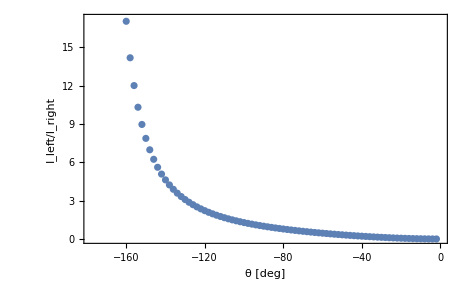

```mathematica
pts=Table[{tmp[[1]],(tmp[[2,1]]{Cos[tmp[[1]]],Sin[tmp[[1]]],0})},{tmp,data}];
(* this computes the intensity ratio: Subscript[I, left]/Subscript[I, right] *)
ListPlot[{#[[1]]180/Pi,(Norm[leds[[2]]-#[[2]]]/Norm[leds[[1]]-#[[2]]])^2}&/@pts,Frame->True,FrameLabel->{"θ [deg]","I_left/I_right"},PlotRange->Automatic]
```

Since the function is monotonic, it should be possible to uniquely determine d and θ, by knowing the angle between the two LEDs and the ratio of their intensities on the camera sensor.

## Misc Geometry - 3 LEDS

What is shown here:

1) we put the LED bar center in the origin, aligned along the x axis
2) the gun (viewpoint) sees the two LEDS at a given angle γ
3) the gun is located at some point (d,θ) in polar coordinates
4) we find the distance d that satisfies (2)

```mathematica
org={0,0,0};
h=.;(* distance between LED and center of bar *)
d=.;
leds={org,org+{h,0,0},org+{0,0,h}};(* LED positions *)
p=d{Cos[θ]Cos[ϕ],Sin[θ]Cos[ϕ],Sin[ϕ]}; (* gun position *)
v=(#-p)&/@leds;(* vectors gun->LEDs *)
Subscript[I, RO]=(Norm[v[[1]]]^2/Norm[v[[2]]]^2);
Subscript[I, TO]=d^2/(d^2+h^2-2 d h Sin[ϕ]);(Norm[v[[1]]]^2/Norm[v[[3]]]^2);

eqx=v[[1]].v[[2]]/(Norm[v[[1]]]Norm[v[[2]]]);
eqy=v[[1]].v[[3]]/(Norm[v[[1]]]Norm[v[[3]]]);
solx=Solve[eqx==Cos[γ],d]//FullSimplify
soly=Solve[eqy==Cos[δ],d]
```

{{d→h Cos[θ] Cos[ϕ]+1/4 Csc[γ]^2 √(-h^2 (-3+2 Cos[2 θ] Cos[ϕ]^2+Cos[2 ϕ]) Sin[2 γ]^2)},{d→h Cos[θ] Cos[ϕ]-1/4 Csc[γ]^2 √(-h^2 (-3+2 Cos[2 θ] Cos[ϕ]^2+Cos[2 ϕ]) Sin[2 γ]^2)}}

{{d→h Cos[δ-ϕ] Csc[δ]},{d→-h Cos[δ+ϕ] Csc[δ]}}

```mathematica
Manipulate[
Show[{
ListPointPlot3D[{org}, PlotStyle->Directive[{Black,PointSize[Medium]}]],
ListPointPlot3D[leds/.{h->0.1}, PlotStyle->Directive[{Red,PointSize[Medium]}]],
ListPointPlot3D[{p/.{θ->t Degree,ϕ->f Degree,d->r}}, PlotStyle->Directive[{Blue,PointSize[Large]}]],
ParametricPlot3D[r{Sin[u],-Cos[u],0},{u,-Pi/2,Pi/2}],
Graphics3D[Inset["I_TO: "<>ToString[Subscript[I, TO]/.{θ->t Degree,ϕ->f Degree,d->r,h->0.1}],{0,0,0.1}+p/.{θ->t Degree,ϕ->f Degree,d->r}]],
Graphics3D[Inset["I_RO: "<>ToString[Subscript[I, RO]/.{θ->t Degree,ϕ->f Degree,d->r,h->0.1}],{0,0,-0.1}+p/.{θ->t Degree,ϕ->f Degree,d->r}]]
},AxesLabel->{"x","y","z"},PlotRange->{{-r,r},{-r,r},{-0.2,1}},AspectRatio->1]

,{{t,-90},0,-180},{{f,0},-90,90},{{r,3},1,4}]
```

ListPointPlot3D::ldata: {p} is not a valid dataset or list of datasets.

Show::gcomb: Could not combine the graphics objects in ….

ListPointPlot3D::ldata: {org} is not a valid dataset or list of datasets.

ListPointPlot3D::ldata: leds is not a valid dataset or list of datasets.

General::stop: Further output of ListPointPlot3D::ldata will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

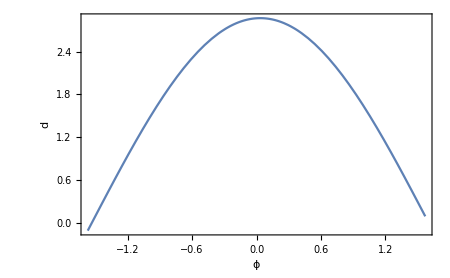

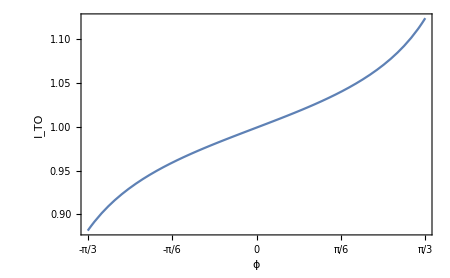

```mathematica
δ0=2.0Degree;(* assume some value for the vertical angle under which LEDs 3/1 are seen *)
tmpy=soly/.{δ->δ0};(* multiple values of d/ϕ are allowed, and any value of θ is also good *)
Plot[{(tmpy[[1]]/.{h->0.1})[[1,2]]},{ϕ,-Pi/2,Pi/2},FrameLabel->{"ϕ","d"}]
(* but intensity ratio would change with ϕ *)
Plot[(Subscript[I, TO]/.{tmpy[[1,1]]})/.{h->0.1},{ϕ,-Pi/3,Pi/3},FrameLabel->{"ϕ","I_TO"},PlotRange->All,FrameTicks->{{Automatic,Automatic},{Table[a,{a,-Pi/3,Pi/3,Pi/6}],Automatic}}]
```

```mathematica
Print["This is the distance assuming we see the LEDs T/O under and angle δ:"];soly[[1,1]]
Print["This is the T/O intensity ratio we get at that distance, depending on vertical angle:"];ItoAtdOfdelta=(Subscript[I, TO]/.{soly[[1,1]]})//FullSimplify
Print["We can invert it to get the ϕ as a function of the measured ratio:"];
Solve[{ItoAtdOfdelta==Itocam},ϕ]
Print["and we can plot it"];
Plot3D[{-ArcTan[(-√Itocam+Cos[δ Degree]) Csc[δ Degree]]180/Pi,-ArcTan[(√Itocam+Cos[δ Degree]) Csc[δ Degree]]180/Pi},{Itocam,0.5,1.5},{δ,0.1,5},AxesLabel->{"I_TO","δ [°]","ϕ [°]"}]
```

This is the distance assuming we see the LEDs T/O under and angle δ:

d→h Cos[δ-ϕ] Csc[δ]

This is the T/O intensity ratio we get at that distance, depending on vertical angle:

(Cos[δ]+Sin[δ] Tan[ϕ])^2

We can invert it to get the ϕ as a function of the measured ratio:

{{ϕ→ConditionalExpression[-ArcTan[(-√Itocam+Cos[δ]) Csc[δ]]+π C[1],C[1]∈Integers]},{ϕ→ConditionalExpression[-ArcTan[(√Itocam+Cos[δ]) Csc[δ]]+π C[1],C[1]∈Integers]}}

and we can plot it

-Graphics3D-

```mathematica
Print["We linearize it around the ϕ=0 for simplicity:"];ItoAtdOfdeltaLIN=((ItoAtdOfdelta+dϕ D[ItoAtdOfdelta,ϕ])/.{ϕ->0})//FullSimplify
Print["and solve:"];
Solve[{ItoAtdOfdeltaLIN==Itocam},dϕ][[1,1]]
Print["and plot:"];
Plot3D[-180/Pi 1/2 (-Itocam+Cos[δ Degree]^2) Csc[δ Degree] Sec[δ Degree],{Itocam,0.5,1.5},{δ,0.1,5},AxesLabel->{"I_TO","δ [°]","ϕ [°]"}]
```

We linearize it around the ϕ=0 for simplicity:

Cos[δ] (Cos[δ]+2 dϕ Sin[δ])

and solve:

dϕ→-1/2 (-Itocam+Cos[δ]^2) Csc[δ] Sec[δ]

and plot:

-Graphics3D-

```mathematica
Plot3D[{-ArcTan[(-√Itocam+Cos[δ Degree]) Csc[δ Degree]]180/Pi,-180/Pi 1/2 (-Itocam+Cos[δ Degree]^2) Csc[δ Degree] Sec[δ Degree]},{Itocam,0.9,1.1},{δ,0.1,5},AxesLabel->{"I_TO","δ [°]","ϕ [°]"},PlotPoints->30,Mesh->None,PlotRange->Automatic]
```

-Graphics3D-

```mathematica
(* plots the difference bwetween full and linearised solutions *)
Plot3D[{-ArcTan[(-√Itocam+Cos[δ Degree]) Csc[δ Degree]]+1/2 (-Itocam+Cos[δ Degree]^2) Csc[δ Degree] Sec[δ Degree]},{Itocam,0.95,1.05},{δ,0.1,5},AxesLabel->{"I_TO","δ [°]","ϕ [°]"},PlotPoints->30,PlotRange->Automatic]
```

-Graphics3D-

The linear model is OK as long as:
1. we are not too far from the LEDs, so the angle δ is not too small
2. the intensity ratio is not too far from 1, which means the vertical angle ϕ is not too large

(2) is always satisfied in practice since the intensity ratio changed only by ~0.01 between -30 and 30 degrees.

5.71059

(d^2 Cos[θ]^2 Cos[ϕ]^2+d^2 Cos[ϕ]^2 Sin[θ]^2-d Sin[ϕ] (h-d Sin[ϕ]))/(√(Abs[d Cos[θ] Cos[ϕ]]^2+Abs[d Cos[ϕ] Sin[θ]]^2+Abs[d Sin[ϕ]]^2) √(Abs[d Cos[θ] Cos[ϕ]]^2+Abs[d Cos[ϕ] Sin[θ]]^2+Abs[h-d Sin[ϕ]]^2))

-Graphics3D-

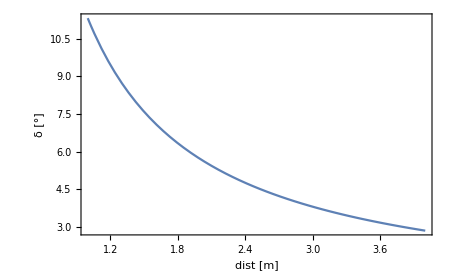

```mathematica
ArcTan[0.1]180/Pi
v[[1]].v[[3]]/Norm[v[[1]]]/Norm[v[[3]]]
Plot3D[ArcCos[(v[[1]].v[[3]]/Norm[v[[1]]]/Norm[v[[3]]])]180/Pi/.{θ->0,h->0.2},{ϕ,-Pi/2,Pi/2},{d,1,4},AxesLabel->{"ϕ [rad]","dist [m]","δ [°]"}]
Plot[ArcCos[(v[[1]].v[[3]]/Norm[v[[1]]]/Norm[v[[3]]])]180/Pi/.{θ->0,h->0.2,ϕ->0},{d,1,4},FrameLabel->{"dist [m]","δ [°]"}]
```

## Simulator

#### Player setup

```mathematica
armlen=0.60;
playerHeight=1.6;
playerDist=-3.0;
player={-0.0,playerDist,playerHeight};
```

#### Screen setup

```mathematica
screenh=playerHeight;(* height of the screen center from the ground *)
screen=0.05;(* screen size factor *)
screenx=16 screen;
screeny=10 screen;
Print["Screen size: "<>ToString[{screenx,screeny}]];
(* screen polygon area *)
screenpoly={{-screenx/2,0,-screeny/2},{screenx/2,0,-screeny/2},{screenx/2,0,screeny/2},{-screenx/2,0,screeny/2}};
screenpoly[[All,3]]+=screenh;
```

Screen size: {0.8, 0.5}

#### LEDs setup

```mathematica
org={0,0,playerHeight};(* center of the LED bar *)
org={0,0,playerHeight};
h=0.1;(* distance between LED and center of bar *)
leds={org-{h,0,0},org+{h,0,0}};(* LED positions *)
```

### visualiser

```mathematica
Manipulate[
gundir={Sin[ϕ],Cos[θ]Cos[ϕ],Sin[θ]Cos[ϕ]};
gunpos=player+armlen gundir;
hitfactor=Solve[(player+(armlen+λ) gundir)[[2]]==0,λ][[1,1,2]];
led1dir=leds[[1]]-gunpos;
led2dir=leds[[2]]-gunpos;
Show[{
Plot3D[0,{x,-5,5},{z,-5,5},AxesLabel->{"x","y","z"},ColorFunction->White,Lighting->"Neutral"],
Graphics3D[Cylinder[{player{1,1,0},player},0.2]],
Graphics3D[Cylinder[{player,gunpos},0.05]],
Graphics3D[Polygon[screenpoly]],Graphics3D[{Red,Line[{gunpos,gunpos+gundir 10}]}],
ListPointPlot3D[{org},PlotStyle->Red],
ListPointPlot3D[leds,PlotStyle->Blue],
ListPointPlot3D[{gunpos+hitfactor gundir},PlotStyle->Green],
Graphics3D[{Blue,Line[{gunpos,gunpos+led1dir 10}]}],
Graphics3D[{Blue,Line[{gunpos,gunpos+led2dir 10}]}],
ListPointPlot3D[{player}]
},PlotRange->{{-1,1},{-3,0},{0,3}},BoxRatios->{2,3,3}]

,{{θ,0},-20Degree,20Degree},{{ϕ,0},-20Degree,20Degree}]
```

Part::partd: Part specification leds⟦1⟧ is longer than depth of object.

Part::partd: Part specification leds⟦2⟧ is longer than depth of object.

ListPointPlot3D::ldata: {org} is not a valid dataset or list of datasets.

ListPointPlot3D::ldata: leds is not a valid dataset or list of datasets.

General::stop: Further output of ListPointPlot3D::ldata will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

```mathematica
gundir={Sin[ϕ],Cos[θ]Cos[ϕ],Sin[θ]Cos[ϕ]};
Solve[(player+(armlen+λ) gundir)[[2]]==0,λ][[1,1,2]]
```

(2.5-0.6 Cos[θ] Cos[ϕ]) Sec[θ] Sec[ϕ]

### mist steps

```mathematica
gunz={Sin[ϕ],Cos[θ]Cos[ϕ],Sin[θ]Cos[ϕ]}
```

{Sin[π/18],Cos[π/18],0}

```mathematica
gunx=RotationMatrix[γ,gunz]
```

{{(2 Cos[π/18]^2+Cos[π/18]^2 Cot[π/18]^2+Sin[π/18]^2)/((1+Cot[π/18]^2) (Cos[π/18]^2+Sin[π/18]^2)),0,0},{0,(2 Cos[π/18]^2+Cos[π/18]^2 Cot[π/18]^2+Sin[π/18]^2)/((1+Cot[π/18]^2) (Cos[π/18]^2+Sin[π/18]^2)),0},{0,0,1}}

```mathematica
shlx=RotationMatrix[ϕ,{0,0,1}].{1,0,0}
faceFwd=RotationMatrix[ϕ,{0,0,1}].{0,1,0}
armFwd=FullSimplify[RotationMatrix[θ,shlx].faceFwd,{θ,ϕ}∈Reals];
armFwd={-Cos[θ] Sin[ϕ],Cos[θ] Cos[ϕ],Sin[θ]}
```

{Cos[π/18],Sin[π/18],0}

{-Sin[π/18],Cos[π/18],0}

{-Sin[π/18],Cos[π/18],0}

```mathematica
FullSimplify[RotationMatrix[γ,armFwd],{θ,ϕ,γ}∈Reals];
```

```mathematica
rotmat={{(Cos[θ]^2+Cos[γ] Cot[ϕ]^2+(Cos[γ] Sin[θ]^2)/1)/Csc[ϕ]^2,-(2 Cos[θ]^2 Cot[ϕ] Sin[γ/2]^2)/Csc[ϕ]^2-Sin[γ] Sin[θ],Cos[θ] (Cot[ϕ] Sin[γ]-2 Sin[γ/2]^2 Sin[θ]) Sin[ϕ]},{-(2 Cos[θ]^2 Cot[ϕ] Sin[γ/2]^2)/Csc[ϕ]^2+Sin[γ] Sin[θ],(Cos[γ]+Cos[θ]^2 Cot[ϕ]^2+Cos[γ] Cot[ϕ]^2 Sin[θ]^2)/Csc[ϕ]^2,Cos[θ] (Sin[γ]+2 Cot[ϕ] Sin[γ/2]^2 Sin[θ]) Sin[ϕ]},{-Cos[θ] (Cot[ϕ] Sin[γ]+2 Sin[γ/2]^2 Sin[θ]) Sin[ϕ],-Cos[θ] (Sin[γ]-2 Cot[ϕ] Sin[γ/2]^2 Sin[θ]) Sin[ϕ],Cos[γ/2]^2-Cos[2 θ] Sin[γ/2]^2}}//FullSimplify;
```

```mathematica
gunx=rotmat.shlx
```

{Cos[π/18],Sin[π/18],0}

```mathematica
gunUp=Cross[gunx,gunz];
gunz==armFwd
```

False

```mathematica
Remove[gunUp];
gunUpv[θ_,ϕ_,γ_]:={Cos[θ]^2 Cos[ϕ]^3 Sin[γ]+Cos[ϕ]^2 Sin[γ] Sin[θ]^2+Cos[θ]^2 Cos[ϕ]^3 Sin[θ] Sin[ϕ]-2 Cos[θ]^2 Cos[ϕ]^3 Sin[γ/2]^2 Sin[θ] Sin[ϕ]+Cos[γ] Cos[ϕ]^3 Sin[θ]^3 Sin[ϕ]+Cos[θ]^2 Cos[ϕ] Sin[γ] Sin[ϕ]^2+Cos[γ] Cos[ϕ] Sin[θ] Sin[ϕ]^3,-Cos[γ] Cos[ϕ]^4 Sin[θ]-Cos[θ] Cos[ϕ]^2 Sin[γ] Sin[ϕ]+Cos[ϕ] Sin[γ] Sin[θ]^2 Sin[ϕ]-Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]^2+2 Cos[θ]^2 Cos[ϕ]^2 Sin[γ/2]^2 Sin[θ] Sin[ϕ]^2-Cos[γ] Cos[ϕ]^2 Sin[θ]^3 Sin[ϕ]^2-Cos[θ] Sin[γ] Sin[ϕ]^3,Cos[γ] Cos[θ] Cos[ϕ]^4-Cos[ϕ] Sin[γ] Sin[θ] Sin[ϕ]-Cos[θ] Cos[ϕ] Sin[γ] Sin[θ] Sin[ϕ]-Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2+Cos[θ]^3 Cos[ϕ]^2 Sin[ϕ]^2+2 Cos[θ]^2 Cos[ϕ]^2 Sin[γ/2]^2 Sin[ϕ]^2-2 Cos[θ]^3 Cos[ϕ]^2 Sin[γ/2]^2 Sin[ϕ]^2-Cos[γ] Cos[ϕ]^2 Sin[θ]^2 Sin[ϕ]^2+Cos[γ] Cos[θ] Cos[ϕ]^2 Sin[θ]^2 Sin[ϕ]^2-Cos[γ] Sin[ϕ]^4}
gunUp[θ_,ϕ_,γ_]:=gunUpv[θ,ϕ,γ]/Norm[gunUpv[θ,ϕ,γ]]
```

```mathematica
Remove[gunx];
gunx[θ_,ϕ_,γ_]:={Cos[ϕ] (Cos[θ]^2+Cos[γ] (Cot[ϕ]^2+Sin[θ]^2)) Sin[ϕ]^2+Sin[ϕ] (-Sin[γ] Sin[θ]-2 Cos[θ]^2 Cos[ϕ] Sin[γ/2]^2 Sin[ϕ]),(Cos[γ]+Cos[θ]^2 Cot[ϕ]^2+Cos[γ] Cot[ϕ]^2 Sin[θ]^2) Sin[ϕ]^3+Cos[ϕ] (Sin[γ] Sin[θ]-2 Cos[θ]^2 Cos[ϕ] Sin[γ/2]^2 Sin[ϕ]),-Cos[θ] Cos[ϕ] (Cot[ϕ] Sin[γ]+2 Sin[γ/2]^2 Sin[θ]) Sin[ϕ]-Cos[θ] (Sin[γ]-2 Cot[ϕ] Sin[γ/2]^2 Sin[θ]) Sin[ϕ]^2}
```

```mathematica
Remove[armFwd]
```

```mathematica
armFwd[θ_,ϕ_]:={-Cos[θ] Sin[ϕ],Cos[θ] Cos[ϕ],Sin[θ]};
```

```mathematica
Dynamic[armFwd];
Manipulate[
gundir={Sin[ϕ],Cos[θ]Cos[ϕ],Sin[θ]Cos[ϕ]};
gunpos=player+armlen gundir;
hitfactor=Solve[(player+(armlen+λ) gundir)[[2]]==0,λ][[1,1,2]];
led1dir=leds[[1]]-gunpos;
led2dir=leds[[2]]-gunpos;
Show[{
Plot3D[0,{x,-5,5},{z,-5,5},AxesLabel->{"x","y","z"},ColorFunction->White,Lighting->"Neutral"],
Graphics3D[Cylinder[{player{1,1,0},player},0.2]],
Graphics3D[Cylinder[{player,gunpos},0.05]],
Graphics3D[Polygon[screenpoly]],Graphics3D[{Red,Line[{gunpos,gunpos+gundir 10}]}],
ListPointPlot3D[{org},PlotStyle->Red],
ListPointPlot3D[leds,PlotStyle->Blue],
ListPointPlot3D[{gunpos+hitfactor gundir},PlotStyle->Green],
Graphics3D[{Blue,Line[{gunpos,gunpos+led1dir 10}]}],
Graphics3D[{Blue,Line[{gunpos,gunpos+led2dir 10}]}],
ListPointPlot3D[{player}],
Graphics3D[{Blue,Arrow[{gunpos,gunpos+armFwd[θ,-ϕ]}]}],
Graphics3D[{Green,Arrow[{gunpos,gunpos+gunUp[θ,-ϕ,γ]}]}],
Graphics3D[{Red,Arrow[{gunpos,gunpos+gunx[θ,-ϕ,γ]}]}],
Graphics3D[Inset[gunx[θ,-ϕ,γ],{1,1,1}]]
},PlotRange->{{-1,1},{-3,0},{0,3}},BoxRatios->{2,3,3}]

,{{θ,0},-20Degree,20Degree},{{ϕ,0},-20Degree,20Degree},{{γ,0},-20Degree,20Degree}]
```

Part::partd: Part specification leds⟦1⟧ is longer than depth of object.

Part::partd: Part specification leds⟦2⟧ is longer than depth of object.

ListPointPlot3D::ldata: {org} is not a valid dataset or list of datasets.

ListPointPlot3D::ldata: leds is not a valid dataset or list of datasets.

General::stop: Further output of ListPointPlot3D::ldata will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

```mathematica
gunx[θ,-ϕ,γ]
```

{Cos[π/18] (1+Cot[π/18]^2) Sin[π/18]^2,-(1+Cot[π/18]^2) Sin[π/18]^3,0}

```mathematica
Manipulate[
armFwd
,{{θ,0},-20Degree,20Degree},{{ϕ,0},-20Degree,20Degree},{{γ,0},-20Degree,20Degree}]
```

### Reference System

Forward direction of the gun

```mathematica
gunFwd[θ_,ϕ_]:={-Sin[ϕ],Cos[θ]Cos[ϕ],Sin[θ]Cos[ϕ]}
```

Up direction of the gun

```mathematica
gunUpv[θ_,ϕ_,γ_]:={Cos[θ]^2 Cos[ϕ]^3 Sin[γ]+Cos[ϕ]^2 Sin[γ] Sin[θ]^2+Cos[θ]^2 Cos[ϕ]^3 Sin[θ] Sin[ϕ]-2 Cos[θ]^2 Cos[ϕ]^3 Sin[γ/2]^2 Sin[θ] Sin[ϕ]+Cos[γ] Cos[ϕ]^3 Sin[θ]^3 Sin[ϕ]+Cos[θ]^2 Cos[ϕ] Sin[γ] Sin[ϕ]^2+Cos[γ] Cos[ϕ] Sin[θ] Sin[ϕ]^3,-Cos[γ] Cos[ϕ]^4 Sin[θ]-Cos[θ] Cos[ϕ]^2 Sin[γ] Sin[ϕ]+Cos[ϕ] Sin[γ] Sin[θ]^2 Sin[ϕ]-Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]^2+2 Cos[θ]^2 Cos[ϕ]^2 Sin[γ/2]^2 Sin[θ] Sin[ϕ]^2-Cos[γ] Cos[ϕ]^2 Sin[θ]^3 Sin[ϕ]^2-Cos[θ] Sin[γ] Sin[ϕ]^3,Cos[γ] Cos[θ] Cos[ϕ]^4-Cos[ϕ] Sin[γ] Sin[θ] Sin[ϕ]-Cos[θ] Cos[ϕ] Sin[γ] Sin[θ] Sin[ϕ]-Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2+Cos[θ]^3 Cos[ϕ]^2 Sin[ϕ]^2+2 Cos[θ]^2 Cos[ϕ]^2 Sin[γ/2]^2 Sin[ϕ]^2-2 Cos[θ]^3 Cos[ϕ]^2 Sin[γ/2]^2 Sin[ϕ]^2-Cos[γ] Cos[ϕ]^2 Sin[θ]^2 Sin[ϕ]^2+Cos[γ] Cos[θ] Cos[ϕ]^2 Sin[θ]^2 Sin[ϕ]^2-Cos[γ] Sin[ϕ]^4}
gunUp[θ_,ϕ_,γ_]:=gunUpv[θ,ϕ,γ]/Norm[gunUpv[θ,ϕ,γ]]
```

Gun right vector

```mathematica
gunRight[θ_,ϕ_,γ_]:=If[ϕ==0,{Cos[γ],0,-Sin[γ]},{Cos[ϕ] (Cos[θ]^2+Cos[γ] (Cot[ϕ]^2+Sin[θ]^2)) Sin[ϕ]^2+Sin[ϕ] (-Sin[γ] Sin[θ]-2 Cos[θ]^2 Cos[ϕ] Sin[γ/2]^2 Sin[ϕ]),(Cos[γ]+Cos[θ]^2 Cot[ϕ]^2+Cos[γ] Cot[ϕ]^2 Sin[θ]^2) Sin[ϕ]^3+Cos[ϕ] (Sin[γ] Sin[θ]-2 Cos[θ]^2 Cos[ϕ] Sin[γ/2]^2 Sin[ϕ]),-Cos[θ] Cos[ϕ] (Cot[ϕ] Sin[γ]+2 Sin[γ/2]^2 Sin[θ]) Sin[ϕ]-Cos[θ] (Sin[γ]-2 Cot[ϕ] Sin[γ/2]^2 Sin[θ]) Sin[ϕ]^2}]
```

```mathematica
Manipulate[
gundir={Sin[ϕ],Cos[θ]Cos[ϕ],Sin[θ]Cos[ϕ]};
gunpos=player+armlen gundir;
hitfactor=Solve[(player+(armlen+λ) gundir)[[2]]==0,λ][[1,1,2]];
led1dir=leds[[1]]-gunpos;
led2dir=leds[[2]]-gunpos;
Show[{
Plot3D[0,{x,-5,5},{z,-5,5},AxesLabel->{"x","y","z"},ColorFunction->White,Lighting->"Neutral"],
Graphics3D[Cylinder[{player{1,1,0},player},0.2]],
Graphics3D[Cylinder[{player,gunpos},0.05]],
Graphics3D[Polygon[screenpoly]],Graphics3D[{Red,Line[{gunpos,gunpos+gundir 10}]}],
ListPointPlot3D[{org},PlotStyle->Red],
ListPointPlot3D[leds,PlotStyle->Blue],
ListPointPlot3D[{gunpos+hitfactor gundir},PlotStyle->Green],
Graphics3D[{Blue,Line[{gunpos,gunpos+led1dir 10}]}],
Graphics3D[{Blue,Line[{gunpos,gunpos+led2dir 10}]}],
Graphics3D[{Blue,Arrow[{gunpos,gunpos+gunFwd[θ,-ϕ]}]}],
Graphics3D[{Green,Arrow[{gunpos,gunpos+gunUp[θ,-ϕ,γ]}]}],
Graphics3D[{Red,Arrow[{gunpos,gunpos+gunRight[θ,-ϕ,γ]}]}],
(*Graphics3D[Inset[gunx[θ,-ϕ,γ],{1,1,1}]],*)
ListPointPlot3D[{player}]
},PlotRange->{{-1,1},{-3,0},{0,3}},BoxRatios->{2,3,3}]

,{{θ,0},-20Degree,20Degree},{{ϕ,0},-20Degree,20Degree},{{γ,0},-20Degree,20Degree}]
```

Part::partd: Part specification leds⟦1⟧ is longer than depth of object.

Part::partd: Part specification leds⟦2⟧ is longer than depth of object.

ListPointPlot3D::ldata: {org} is not a valid dataset or list of datasets.

ListPointPlot3D::ldata: leds is not a valid dataset or list of datasets.

General::stop: Further output of ListPointPlot3D::ldata will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

```mathematica
Manipulate[

θ=θr*Pi/180;
ϕ=ϕr*Pi/180;
γ=γr*Pi/180;

gundir={Sin[ϕ],Cos[θ]Cos[ϕ],Sin[θ]Cos[ϕ]};
gunpos=player+armlen gundir;
hitfactor=Solve[(player+(armlen+λ) gundir)[[2]]==0,λ][[1,1,2]];
led1dir=leds[[1]]-gunpos;
led2dir=leds[[2]]-gunpos;
mat={gunRight[θ,-ϕ,γ],gunFwd[θ,-ϕ],gunUp[θ,-ϕ,γ]};

led1dirGUN=LinearSolve[Transpose[mat],led1dir][[{1,3}]];
led2dirGUN=LinearSolve[Transpose[mat],led2dir][[{1,3}]];
ledDist=Norm[led2dirGUN-led1dirGUN];
Iratio12=(Norm[gunpos-leds[[2]]]/Norm[gunpos-leds[[1]]])^2;
I1=1/Norm[gunpos-leds[[1]]]^2;
I2=1/Norm[gunpos-leds[[2]]]^2;

(* screenpoly *)
screencorners=(#-gunpos)&/@screenpoly;
screencornersGUN=LinearSolve[Transpose[mat],#][[{1,3}]]&/@screencorners;

(*MatrixForm[{
LinearSolve[Transpose[{gunRight[θ,-ϕ,γ],gunFwd[θ,-ϕ],gunUp[θ,-ϕ,γ]}],led1dir],
LinearSolve[Transpose[{gunRight[θ,-ϕ,γ],gunFwd[θ,-ϕ],gunUp[θ,-ϕ,γ]}],led2dir],
LinearSolve[Transpose[{gunRight[θ,-ϕ,γ],gunFwd[θ,-ϕ],gunUp[θ,-ϕ,γ]}],{1,0,0}]
}];*)
roll=ArcCos[{0,1}.(led1dirGUN-led2dirGUN)/ledDist]180/Pi-90;

Show[{ListPlot[{{-0.5,-1},{0.5,1}}],
Graphics[{Red,PointSize[0.1I1],Point[led1dirGUN]}],
Graphics[{Red,PointSize[0.1I2],Point[led2dirGUN]}],
Graphics[Inset["LED dist="<>ToString[led2dirGUN-led1dirGUN]<>" - "<>ToString[ledDist],{0.2,0.5}]],
Graphics[Inset["roll="<>ToString[roll]<>"Δ%="<>ToString[Chop[100(roll-γr)/(γr+10^-10)]],{0.2,-0.5}]],
Graphics[Inset["Ir="<>ToString[Iratio12],{-0.4,0.2}]],
Graphics[Inset[ledDist,{-0.4,0.5}]],
Graphics[{Opacity[0.5],Gray,Polygon[screencornersGUN]}]
},PlotRange->All]

,{{θr,0},-20,20},{{ϕr,0},-20,20},{{γr,0},-20,20}]
```

Part::partd: Part specification leds⟦1⟧ is longer than depth of object.

Part::partd: Part specification leds⟦2⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {gunRight[0,0,0],gunFwd[0,0],gunUp[0,0,0]} cannot be transposed.

Part::partw: Part {1,3} of LinearSolve[Transpose[{gunRight[0,0,0],gunFwd[0,0],gunUp[0,0,0]}],{-player+leds⟦1⟧,-armlen-player+leds⟦1⟧,-player+leds⟦1⟧}] does not exist.

Transpose::nmtx: The first two levels of {gunRight[0,0,0],gunFwd[0,0],gunUp[0,0,0]} cannot be transposed.

Part::partw: Part {1,3} of LinearSolve[Transpose[{gunRight[0,0,0],gunFwd[0,0],gunUp[0,0,0]}],{-player+leds⟦2⟧,-armlen-player+leds⟦2⟧,-player+leds⟦2⟧}] does not exist.

Part::partw: Part {1,3} of LinearSolve[Transpose[{gunRight[0,0,0],gunFwd[0,0],gunUp[0,0,0]}],{-player+leds⟦1⟧,-armlen-player+leds⟦1⟧,-player+leds⟦1⟧}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification leds⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

### Generate camera image from known parameters

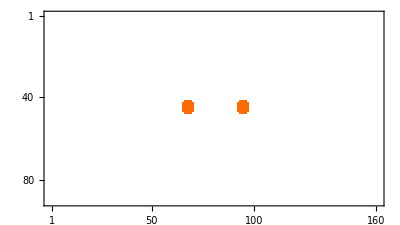

{1→{7.45513,{67.,44.5},3.3541},2→{7.45513,{94.,44.5},3.3541}}

{7.45513,7.45513}

27.

{{67.,44.5},{94.,44.5}}

{80.5,44.5}

27.

```mathematica
(* generate a camera image from known coordinates and directions *)
θ=-0*Pi/180;
ϕ=-0*Pi/180;
γ=0*Pi/180;

player={0,-2,playerHeight};

ledsize=0.025;
fov=48.5*Pi/180.;
xres=320/2;
yres=180/2;
radPerPx=fov/xres;

gundir={Sin[ϕ],Cos[θ]Cos[ϕ],Sin[θ]Cos[ϕ]};(* camera view direction *)
gunpos=player+armlen gundir;(* camera position *)
hitfactor=Solve[(player+(armlen+λ) gundir)[[2]]==0,λ][[1,1,2]];
led1dir=leds[[1]]-gunpos;
led2dir=leds[[2]]-gunpos;
mat={gunRight[θ,-ϕ,γ],gunFwd[θ,-ϕ],gunUp[θ,-ϕ,γ]};

led1dirGUN=LinearSolve[Transpose[mat],led1dir][[{1,3}]];
led2dirGUN=LinearSolve[Transpose[mat],led2dir][[{1,3}]];
ledDist=Norm[led2dirGUN-led1dirGUN];

tmp=Table[(* does this hit the LED disk? *)
gunray={Sin[ϕ+p],Cos[θ+t]Cos[ϕ+p],Sin[θ+t]Cos[ϕ+p]};
hits=Table[
a=gunray.gunray;
b=2gunray.(gunpos-led);
c=(gunpos-led).(gunpos-led)-ledsize^2;
delta=b^2-4a c;
If[delta<0,0,1]
,{led,leds}];
hits[[1]]+hits[[2]]
,{t,-radPerPx*yres/2,radPerPx*yres/2-0.0001,radPerPx},{p,-fov*0.5,fov*0.5-0.0001,radPerPx}];
cameraimage=tmp;
MatrixPlot[tmp//Reverse]

spots=ComponentMeasurements[MorphologicalComponents[cameraimage],{"Length","BoundingDiskCenter","BoundingDiskRadius"}];
spots=SortBy[spots,#[[2,2,1]]&]
diam=spots[[All,2,1]]
spotdist=Norm[spots[[2,2,2]]-spots[[1,2,2]]]

Norm[gunpos-#]&/@leds;
(%[[1]]^2+%[[2]]^2-(2ledsize)^2)/(2%[[1]]%[[2]]);
ArcCos[%];
%/radPerPx;
diamcorrect={%,%};

P=spots[[All,2,2]]
M=Mean[P]
m=2h;
mimg=Norm[P[[1]]-P[[2]]]
```

```mathematica
w=m xres/spotdist
d=0.5w/Tan[fov/2]
```

1.18519

1.31551

```mathematica
w=xres 2ledsize/diamcorrect
d=0.5w/Tan[fov/2];(* distances from camera to leds *)
Print["distance camera-leds: "<>ToString[d]];
Print["actual d camera-leds: "<>ToString[Norm[gunpos-#]&/@leds]];
cosphi=(d[[1]]^2m^2-d[[2]]^2)/(2m d[[1]])
dist=Sqrt[d[[1]]^2+(m/2)^2-2d[[1]](m/2)^2cosphi](* distance to midpoint *)
(dist^2m^2-d[[1]]^2)/(m d[[1]]);
ArcCos[(dist^2m^2-d[[1]]^2)/(m d[[1]])];
100(dist-Norm[gunpos-(Mean[leds])])/Norm[gunpos-(Mean[leds])]
```

{1.18804,1.18804}

distance camera-leds: {1.31867, 1.31867}

actual d camera-leds: {1.40357, 1.40357}

-3.16481

1.35365

-3.311

```mathematica
gunpos
Mean[leds]
```

{0.,-2.4,1.6}

{0.,0,1.5}

```mathematica
Norm[gunpos-(Mean[leds])]
```

1.4065

```mathematica
Norm[gunpos-#]&/@leds(* actual gun-led distances *)
Norm[gunpos-(Mean[leds])]
```

{1.40357,1.40357}

1.4

```mathematica
Norm[gunpos-#]&/@leds
(%[[1]]^2+%[[2]]^2-(2ledsize)^2)/(2%[[1]]%[[2]])
ArcCos[%]
%/radPerPx
```

{1.40357,1.40357}

0.999365

0.0356254

6.73381

```mathematica
a=h;
b=1.4;
c=1.40356688476182;
ArcCos[(a^2+b^2-c^2)/(2a b)]180/Pi
```

90.

```mathematica
a=h;
b=dist
c=d[[1]]
ArcCos[(a^2+b^2-c^2)/(2a b)]180/Pi
```

1.38188

1.34632

67.2216

```mathematica
FullSimplify[{x,y}/.Last[Solve[{x^2+y^2==a^2,(x-r)^2+y^2==q^2},{x,y}]]]
{(a^2-q^2+r^2)/(2 r),Sqrt[-(a-q-r) (a+q-r) (a-q+r) (a+q+r)]/(2 r)}
```

```mathematica
Solve[3280/62.2==1280/x,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→24.2732}}

```mathematica
24.273170731707317 2
```

48.5463

### 4-corners

```mathematica
mat={
{x1,y1,1,0,0,0,0,0},
{x2,y2,1,0,0,0,0,0},
{x3,y3,1,0,0,0,-x3,-y3},
{x4,y4,1,0,0,0,-x4,-y4},
{0,0,0,x1,y1,1,0,0},
{0,0,0,x2,y2,1,-x2,-y2},
{0,0,0,x3,y3,1,0,0},
{0,0,0,x4,y4,1,-x4,-y4}
};
MatrixForm[mat]
sols=LinearSolve[mat,{0,0,1,1,0,1,0,1}];
```

(x1 | y1 | 1 | 0 | 0 | 0 | 0 | 0
x2 | y2 | 1 | 0 | 0 | 0 | 0 | 0
x3 | y3 | 1 | 0 | 0 | 0 | -x3 | -y3
x4 | y4 | 1 | 0 | 0 | 0 | -x4 | -y4
0 | 0 | 0 | x1 | y1 | 1 | 0 | 0
0 | 0 | 0 | x2 | y2 | 1 | -x2 | -y2
0 | 0 | 0 | x3 | y3 | 1 | 0 | 0
0 | 0 | 0 | x4 | y4 | 1 | -x4 | -y4)

```mathematica
sols[[1]]//FullSimplify
```

-(((y1-y2) (x4 (y1-y3)+x1 (y3-y4)+x3 (-y1+y4)) (x4 (y2-y3)+x2 (y3-y4)+x3 (-y2+y4)))/(x1 (-x4^2 (y2-y3) (-2 y2 y3+y1 (y2+y3))+2 x3 x4 y2 (y2-y3) (y1-y4)-x3^2 y1 (y2-y4)^2)+x3 x4 (y1-y2)^2 (-x4 y3+x3 y4)+x2 (x4^2 y2 (y1-y3)^2+2 x1 x4 (y2-y3) y3 (y1-y4)-x1^2 y2 (y3-y4)^2-2 x3 (y2-y3) (y1-y4) (x4 y1+x1 y4)+x3^2 (y1-y4) (y1 (y2-2 y4)+y2 y4))+x2^2 (x1 y1 (y3-y4)^2-x4 (y1-y3)^2 y4-x3 (y1-y4) (y1 (y3-2 y4)+y3 y4))+x1^2 (x3 y3 (y2-y4)^2-x4 (y2-y3) (2 y2 y3-(y2+y3) y4))))

```mathematica
sols[[2]]
```

-((x1-x2) (x3-x4))/(-x2 x3 y1+x2 x4 y1+x1 x3 y2-x1 x4 y2+x1 x4 y3-x2 x4 y3-x1 x3 y4+x2 x3 y4)+((x1-x2) (x4 y3-x3 y4) ((-x1 x4 (-x2 y1+x1 y2) (-x1 x2 y1+x1 x3 y1+x1^2 y2-x1 x3 y2-x1^2 y3+x1 x2 y3)+x1 x3 (-x2 y1+x1 y2) ((x1-x4) (-x2 y1+x1 y2)-(x1-x2) (-x4 y1+x1 y4))) (x1 (-x3 y1+x1 y3) (x1 x2 y1-x1 x3 y1-x1^2 y2+x1 x3 y2+x1^2 y3-x1 x2 y3)-x1 (-x3 y1+x1 y3) ((x1-x4) (-x3 y1+x1 y3)-(x1-x3) (-x4 y1+x1 y4)))-(x1 (-x2 y1+x1 y2) (-x1 x2 y1+x1 x3 y1+x1^2 y2-x1 x3 y2-x1^2 y3+x1 x2 y3)-x1 (-x2 y1+x1 y2) ((x1-x4) (-x2 y1+x1 y2)-(x1-x2) (-x4 y1+x1 y4))) (-x1 x4 (-x3 y1+x1 y3) (x1 x2 y1-x1 x3 y1-x1^2 y2+x1 x3 y2+x1^2 y3-x1 x2 y3)+x1 x2 (-x3 y1+x1 y3) ((x1-x4) (-x3 y1+x1 y3)-(x1-x3) (-x4 y1+x1 y4)))))/((-x2 x3 y1+x2 x4 y1+x1 x3 y2-x1 x4 y2+x1 x4 y3-x2 x4 y3-x1 x3 y4+x2 x3 y4) (-(-x1 (-x2 y1+x1 y2) (-x1 x2 y1+x1 x3 y1+x1^2 y2-x1 x3 y2-x1^2 y3+x1 x2 y3) y4+x1 (-x2 y1+x1 y2) y3 ((x1-x4) (-x2 y1+x1 y2)-(x1-x2) (-x4 y1+x1 y4))) (-x1 x4 (-x3 y1+x1 y3) (x1 x2 y1-x1 x3 y1-x1^2 y2+x1 x3 y2+x1^2 y3-x1 x2 y3)+x1 x2 (-x3 y1+x1 y3) ((x1-x4) (-x3 y1+x1 y3)-(x1-x3) (-x4 y1+x1 y4)))+(-x1 x4 (-x2 y1+x1 y2) (-x1 x2 y1+x1 x3 y1+x1^2 y2-x1 x3 y2-x1^2 y3+x1 x2 y3)+x1 x3 (-x2 y1+x1 y2) ((x1-x4) (-x2 y1+x1 y2)-(x1-x2) (-x4 y1+x1 y4))) (-x1 (-x3 y1+x1 y3) (x1 x2 y1-x1 x3 y1-x1^2 y2+x1 x3 y2+x1^2 y3-x1 x2 y3) y4+x1 y2 (-x3 y1+x1 y3) ((x1-x4) (-x3 y1+x1 y3)-(x1-x3) (-x4 y1+x1 y4)))))

```mathematica
sols[[2]]//FullSimplify
```

((x1-x2) (x4 (y1-y3)+x1 (y3-y4)+x3 (-y1+y4)) (x4 (-y2+y3)+x3 (y2-y4)+x2 (-y3+y4)))/(x1 x4^2 (y2-y3) (-2 y2 y3+y1 (y2+y3))-2 x1 x3 x4 y2 (y2-y3) (y1-y4)+x1 x3^2 y1 (y2-y4)^2-x1^2 x3 y3 (y2-y4)^2+x3 x4 (y1-y2)^2 (x4 y3-x3 y4)+x1^2 x4 (y2-y3) (2 y2 y3-(y2+y3) y4)+x2 (-x4^2 y2 (y1-y3)^2-2 x1 x4 (y2-y3) y3 (y1-y4)+x1^2 y2 (y3-y4)^2+2 x3 (y2-y3) (y1-y4) (x4 y1+x1 y4)-x3^2 (y1-y4) (y1 (y2-2 y4)+y2 y4))+x2^2 (-x1 y1 (y3-y4)^2+x4 (y1-y3)^2 y4+x3 (y1-y4) (y1 (y3-2 y4)+y3 y4)))

```mathematica
(* generate a camera image from known coordinates and directions *)
θ=0*Pi/180;
ϕ=10*Pi/180;
γ=0*Pi/180;

player={-1,-3,playerHeight};

ledsize=0.025;
fov=48.5*Pi/180.;
xres=320/2;
yres=180/2;
radPerPx=fov/xres;

gundir={Sin[ϕ],Cos[θ]Cos[ϕ],Sin[θ]Cos[ϕ]};(* camera view direction *)
gunpos=player+armlen gundir;(* camera position *)
hitfactor=Solve[(player+(armlen+λ) gundir)[[2]]==0,λ][[1,1,2]];
led1dir=leds[[1]]-gunpos;
led2dir=leds[[2]]-gunpos;
mat={gunRight[θ,-ϕ,γ],gunFwd[θ,-ϕ],gunUp[θ,-ϕ,γ]};
```

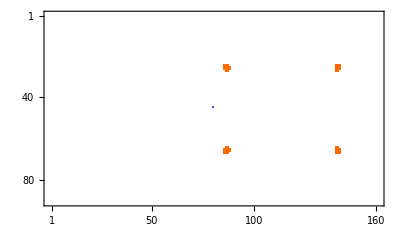

```mathematica
tmp=Table[(* does this hit the LED disk? *)
gunray={Sin[ϕ+p],Cos[θ+t]Cos[ϕ+p],Sin[θ+t]Cos[ϕ+p]};
hits=Table[
a=gunray.gunray;
b=2gunray.(gunpos-led);
c=(gunpos-led).(gunpos-led)-ledsize^2;
delta=b^2-4a c;
If[delta<0,0,1]
,{led,screenpoly}];
Total[hits]
,{t,-radPerPx*yres/2,radPerPx*yres/2-0.0001,radPerPx},{p,-fov*0.5,fov*0.5-0.0001,radPerPx}];
cameraimage=tmp;
tmp[[yres/2,xres/2]]=-1;
MatrixPlot[tmp]
```

```mathematica
spots=ComponentMeasurements[MorphologicalComponents[tmp],{"Length","BoundingDiskCenter","BoundingDiskRadius"}];
spots=SortBy[spots,#[[2,2,1]]+#[[2,2,2]]&][[All,2,2]]
```

{{85.8,24.8},{85.8,64.2},{140.5,25.},{140.5,64.}}

```mathematica
mat={{x1,x2,x3},{y1,y2,y3},{1,1,1}}/.{x1->spots[[1,1]],y1->spots[[1,2]],x2->spots[[2,1]],y2->spots[[2,2]],x3->spots[[3,1]],y3->spots[[3,2]],x4->spots[[4,1]],y4->spots[[4,2]]};
bvec={x4,y4,1}/.{x4->spots[[4,1]],y4->spots[[4,2]]};
MatrixForm[mat]
sol=LinearSolve[mat,bvec];
mat[[All,1]]*=sol[[1]];
mat[[All,2]]*=sol[[2]];
mat[[All,3]]*=sol[[3]];

bmat={{0,0,screenx},{0,screeny,0},{screenx,screeny,1}};
sol=LinearSolve[bmat,{1,1,1}];
bmat[[All,1]]*=sol[[1]];
bmat[[All,2]]*=sol[[2]];
bmat[[All,3]]*=sol[[3]];
mat=Inverse[mat];
cmat=bmat.mat;

cmat.{xres/2,yres/2,1};
%/%[[3]]
cmat.{spots[[1,1]],spots[[1,2]],1};
%/%[[3]]
cmat.{spots[[4,1]],spots[[4,2]],1};
%/%[[3]]
```

(85.8 | 85.8 | 140.5
24.8 | 64.2 | 25.
1 | 1 | 1)

{-0.0934576,0.457,1.}

{1.75832×10^-16,0.,1.}

{1.,1.,1.}

```mathematica
mat={
{x1,y1,1,0,0,0,0,0},
{x2,y2,1,0,0,0,0,0},
{x3,y3,1,0,0,0,-x3 screeny,-y3 screeny},
{x4,y4,1,0,0,0,-x4 screeny,-y4 screeny},
{0,0,0,x1,y1,1,0,0},
{0,0,0,x2,y2,1,-x2 screenx,-y2 screenx},
{0,0,0,x3,y3,1,0,0},
{0,0,0,x4,y4,1,-x4 screenx,-y4 screenx}
};
mat=mat/.{x1->spots[[1,1]],y1->spots[[1,2]],x2->spots[[2,1]],y2->spots[[2,2]],x3->spots[[3,1]],y3->spots[[3,2]],x4->spots[[4,1]],y4->spots[[4,2]]}
MatrixForm[mat]
sols=LinearSolve[mat,{0,0,screeny,screeny,0,screenx,0,screenx}];
sols=Join[sols,{1}];
sols
pmat={
sols[[1;;3]],
sols[[4;;6]],
sols[[7;;9]]
};
MatrixForm[pmat]
pmat.{yres/2,xres/2,0}
```

{{61.8,33.2,1,0,0,0,0,0},{61.8571,72.2857,1,0,0,0,0,0},{123.8,33.2,1,0,0,0,-61.9,-16.6},{123.857,72.2857,1,0,0,0,-61.9286,-36.1429},{0,0,0,61.8,33.2,1,0,0},{0,0,0,61.8571,72.2857,1,-49.4857,-57.8286},{0,0,0,123.8,33.2,1,0,0},{0,0,0,123.857,72.2857,1,-99.0857,-57.8286}}

(61.8 | 33.2 | 1 | 0 | 0 | 0 | 0 | 0
61.8571 | 72.2857 | 1 | 0 | 0 | 0 | 0 | 0
123.8 | 33.2 | 1 | 0 | 0 | 0 | -61.9 | -16.6
123.857 | 72.2857 | 1 | 0 | 0 | 0 | -61.9286 | -36.1429
0 | 0 | 0 | 61.8 | 33.2 | 1 | 0 | 0
0 | 0 | 0 | 61.8571 | 72.2857 | 1 | -49.4857 | -57.8286
0 | 0 | 0 | 123.8 | 33.2 | 1 | 0 | 0
0 | 0 | 0 | 123.857 | 72.2857 | 1 | -99.0857 | -57.8286)

{0.00806452,-0.0000117902,-0.497996,-3.15594×10^-18,0.0204678,-0.679532,-5.19097×10^-18,7.10309×10^-18,1}

(0.00806452 | -0.0000117902 | -0.497996
-3.15594×10^-18 | 0.0204678 | -0.679532
-5.19097×10^-18 | 7.10309×10^-18 | 1)

{0.36196,1.63743,3.34654×10^-16}

```mathematica
pmat=FindGeometricTransform[spots,{{0,0},{1,0},{1,0},{1,1}},TransformationClass->"Perspective"][[2]]
```

TransformationFunction[(-61.8 | 121.836 | 61.8
-33.2 | 71.1064 | 33.2
-1. | 0.983685 | 1.)]

```mathematica
pmat.{yres/2,xres/2,0}
```

TransformationFunction[(-61.8 | 121.836 | 61.8
-33.2 | 71.1064 | 33.2
-1. | 0.983685 | 1.)].{45,80,0}

```mathematica
AffineTransform[{yres/2,xres/2},pmat]
```

AffineTransform::argx: AffineTransform called with 2 arguments; 1 argument is expected.

AffineTransform[{45,80},{48.4566,TransformationFunction[(-61.8 | 121.836 | 61.8
-33.2 | 71.1064 | 33.2
-1. | 0.983685 | 1.)]}]

```mathematica
pmat[{yres/2,xres/2}]
```

{202.558,121.854}

```mathematica
TransformationMatrix[pmat].{yres/2,xres/2,1}
```

{7027.72,4227.71,34.6948}

## FOV tester

Given a screen size, what is the FOV necessary to see both ends from any position/direction?

{11.3099,11.3099}

22.6199

22.6199

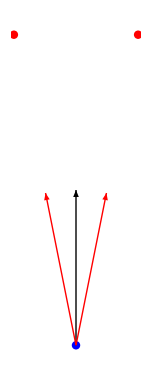

```mathematica
size=0.8;
p={{-size,0},{size,0}}/2;
camera={0,-2};
cameratheta=0+Pi/2;
cameradir={Cos[cameratheta],Sin[cameratheta]};

s=(#-camera)&/@p;
s=(#/Norm[#])&/@s;

angles=(VectorAngle[cameradir,#]&/@s)180/Pi
Total[%]
VectorAngle[s[[1]],s[[2]]]180/Pi

Show[{
Graphics[{PointSize[0.04],Red,Point[#]&/@p,Blue,Point[camera]}],
Graphics[Arrow[{camera,camera+cameradir}]],
Graphics[{Red,Arrow[{camera,camera+#}]&/@s}]
}]
```

```mathematica
MinFOV[size_,camx_,dist_]:=Module[{p,camera,s},
p={{-size,0},{size,0}}/2;
camera={camx,-dist};
s=(#-camera)&/@p;
s=(#/Norm[#])&/@s;
VectorAngle[s[[1]],s[[2]]]180/Pi
]
```

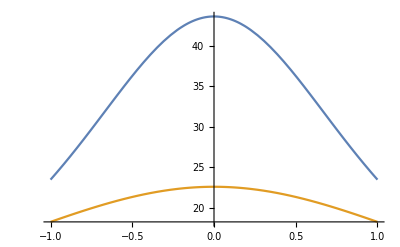

```mathematica
Plot[{MinFOV[0.8,x,1],MinFOV[0.8,x,2]},{x,-1,1},PlotRange->All]
```

```mathematica
Plot3D[MinFOV[0.8,x,d],{x,-1,1},{d,1,3},PlotRange->All]
```

-Graphics3D-